# Bell Violation

## Hong-Ou-Mandel CSCH Inequality - Entangled State & Squeezed State

Valerio Paper 1

Emlyn Graham

Department of Quantum Science

19/08/2018

## Squeezed State - Arbitrary Angle Quadrature

#### Eigenfunctions of Quantum Harmonic Oscillator

We define the useful eigenfunctions and their integrals as follows, as well as setting a λ value and standard finite limit for our sums:

```mathematica
SumLimit := SumLimit = 200.;
SumLimit
```

200.

The standard eigenfunction is defined and the first few plotted:

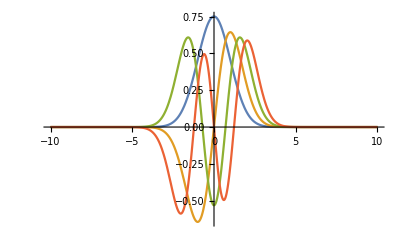

```mathematica
ϕ[n_,x_?NumericQ]:=ϕ[n,x]=FullSimplify[((π^(1./4.)*Sqrt[n!*2.^n])^(-1.))*HermiteH[n,x]*Exp[-(x^2.)/2.]]
Show[Plot[{ϕ[0,x],ϕ[1,x],ϕ[2,x],ϕ[3,x]},{x,-10,10},PlotRange->All]]
```

Checking this is defined properly by seeing that the probabilities sum to 1:

```mathematica
NIntegrate[Abs[Sqrt[(1.-0.83^2.)]*Sum[ϕ[n,x]*ϕ[n,y]*0.83^(n),{n,0,20}]]^2,{x,-10,10},{y,-10,10}]
```

0.999601

```mathematica
ϕθ[n_,y_?NumericQ,θ_?NumericQ]:=ϕθ[n,y,θ]=FullSimplify[((π^(1./4.)*Sqrt[n!*2.^n])^(-1))*HermiteH[n,y]*Exp[-(y^2.)/2.]*Exp[-ⅈ*θ*n]]
```

```mathematica
PXXtheta[x_?NumericQ,y_?NumericQ,θ_?NumericQ,λ_?NumericQ]:=PXXtheta[x,y,θ,λ]=FullSimplify[ComplexExpand[FullSimplify[(((1-λ^2)*Exp[-x^2-y^2])/(π*(Abs[Sqrt[1-(λ^2)*Exp[-2*ⅈ*θ]]]^2)))*Abs[Exp[((λ^2)*Exp[-2*ⅈ*θ]*(x^2+y^2)-2*λ*x*y*Exp[-ⅈ*θ])/((λ^2)*Exp[-2*ⅈ*θ]-1)]]^2,Assumptions->x∈Reals&&y∈Reals&&θ∈Reals&&λ∈Reals&&0≤ λ≤ 1]]]
PXXtheta[x,y,θ,λ]
```

PXXtheta[x,y,θ,λ]

The same will be done with the ENX/EXN terms, as for E(N>0) we have a sum:

```mathematica
E1X[x_?NumericQ,λ_?NumericQ]=FullSimplify[(1.-λ^2.)*(π^(-1/2))*Exp[-x^2]*(((1.-λ^4.)^(-1/2))*Exp[((λ^2.)*((λ^2.)*(2*x^2.)-2*x^2.))/(λ^4. - 1)]-HermiteH[0,x]^2)];
E0X[x_?NumericQ,λ_?NumericQ]=(1.-λ^2.)*Abs[ϕ[0,x]]^2.
```

(1.-λ^2.) Abs[ϕ[0,x]]^2.

#### Probabilities and expectation values

```mathematica
ENN[λ_] = FullSimplify[(1.-λ^2.)*Sum[RealAbs[λ^(2.*n)],{n,0,Infinity}]]
```

-1. (-1.+λ^2.) ∑_(n=0)^∞ RealAbs[λ^(2. n)]

```mathematica
PNX[1,1,z_?NumericQ, λ_?NumericQ]:=PNX[1,1,z, λ]=NIntegrate[E1X[x,λ],{x,-z,z}];
PNX[1,-1,z_?NumericQ, λ_?NumericQ]:=PNX[1,-1,z, λ]=NIntegrate[E1X[x, λ],{x,-Infinity,-z}]+NIntegrate[E1X[x, λ],{x,z,Infinity}];
PNX[-1,1,z_?NumericQ, λ_?NumericQ]:=PNX[-1,1,z, λ]=NIntegrate[E0X[x, λ],{x,-z,z}];
PNX[-1,-1,z_?NumericQ, λ_?NumericQ]:=PNX[-1,-1,z, λ]=NIntegrate[E0X[x, λ],{x,-Infinity,-z}]+NIntegrate[E0X[x, λ],{x,z,Infinity}];
FullSimplify[PNX[1,1,1, 0.83]+PNX[-1,-1,1, 0.83]+PNX[1,-1,1, 0.83]+PNX[-1,1,1, 0.83]]
ENX[z_?NumericQ, λ_?NumericQ]:=ENX[z, λ]=PNX[1,1,z, λ]+PNX[-1,-1,z, λ]-PNX[1,-1,z, λ]-PNX[-1,1,z, λ];
```

1.

```mathematica
N[Integrate[PXXtheta[x,y,0.75, 0.83],{x,-10,10},{y,-10,10}]]
```

1.

```mathematica
ProbXX[1,1,z_?NumericQ,θ_?NumericQ, λ_?NumericQ]:=NIntegrate[PXXtheta[x,y,θ, λ],{x,-z,z},{y,-z,z}];
```

```mathematica
ProbXX[-1,1,z_?NumericQ,θ_?NumericQ, λ_?NumericQ]:=NIntegrate[PXXtheta[x,y,θ, λ],{x,-Infinity,-z},{y,-z,z}]+NIntegrate[PXXtheta[x,y,θ, λ],{x,z,Infinity},{y,-z,z}];
```

```mathematica
ProbXX[1,-1,z_?NumericQ,θ_?NumericQ, λ_?NumericQ]:=NIntegrate[PXXtheta[x,y,θ, λ],{x,-z,z},{y,-Infinity,-z}]+NIntegrate[PXXtheta[x,y,θ, λ],{x,-z,z},{y,z,Infinity}];
```

```mathematica
ProbXX[-1,-1,z_?NumericQ,θ_?NumericQ, λ_?NumericQ]:=NIntegrate[PXXtheta[x,y,θ, λ],{x,-Infinity,-z},{y,-Infinity,-z}]+NIntegrate[PXXtheta[x,y,θ, λ],{x,-Infinity,-z},{y,z,Infinity}]+NIntegrate[PXXtheta[x,y,θ, λ],{x,z,Infinity},{y,-Infinity,-z}]+NIntegrate[PXXtheta[x,y,θ, λ],{x,z,Infinity},{y,z,Infinity}];
```

```mathematica
FullSimplify[ProbXX[1,1,1,π/2, 0.83]+ProbXX[-1,-1,1,π/2, 0.83]+ProbXX[1,-1,1,π/2, 0.83]+ProbXX[-1,1,1,π/2, 0.83]]
EXX[z_?NumericQ,θ_?NumericQ, λ_?NumericQ]:=ProbXX[1,1,z,θ, λ]+ProbXX[-1,-1,z,θ ,λ]-ProbXX[1,-1,z,θ, λ]-ProbXX[-1,1,z,θ, λ];
```

1.

```mathematica
ProbXX[1,1,1,π/2, 0.83]
ProbXX[-1,-1,1,π/2, 0.83]
ProbXX[1,-1,1,π/2, 0.83]
ProbXX[-1,1,1,π/2, 0.83]
```

0.20805

0.2958

0.248075

0.248075

```mathematica
S[z_?NumericQ,θ_?NumericQ, λ_?NumericQ]:=RealAbs[FullSimplify[EXX[z,θ, λ]+2*ENX[z, λ]-1]];
S[0.86,π/2 , 0.83]
```

2.05252

```mathematica
Show[Plot3D[S[z, T, 0.86], {z,0., 10.},{T, 0.,  N[π/2.] }]]
```

$Aborted

```mathematica
globalmax = FindMaximum[{S[z,θ, λ],0.≤ z≤ 20., 0. ≤ θ ≤ N[π/2.], 0.< λ≤ 1.},{{z, 0.86},{θ,N[π/2.]},{λ,0.83}}]
```

{2.05253,{z→0.85826,θ→1.56983,λ→0.827602}}

```mathematica
max = FindMaximum[{S[z,3.141/2.,  λ],0.≤z≤5.,  0≤ λ<1},{z, λ}]
```

{2.05252,{z→0.858112}}

```mathematica
max[[1]]
```

2.05252

```mathematica
NMaximize[{S[z,π/2],0.≤z≤5.},z]
```

{2.05252,{z→0.858112}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

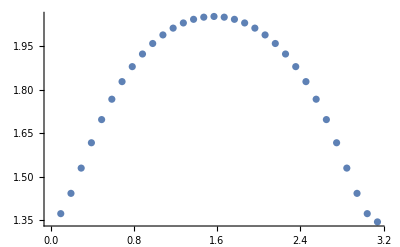

```mathematica
Maxima = Table[{n*π/32,FindMaxValue[{S[z,n*π/32,λ],0≤ z≤ 10},{z,λ}]},{n, 32}];
ListPlot[Maxima]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

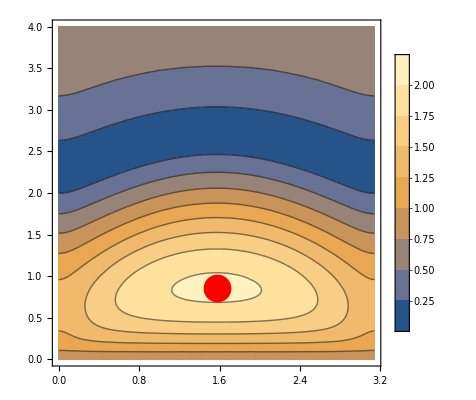

```mathematica
Show[ContourPlot[S[z,θ], {θ,0,N[π]},{z,0,4},Epilog->{PointSize[0.05],Red,Point[{θ,z}/.Last[globalmax]]}, PlotRange->All, PlotLegends->Automatic]]
```